```mathematica
eq1=(r*b[r]*c[r]*a'[r]^2-2r*a[r]*b[r]*c[r]*a''[r]+r*a[r]*c[r]*a'[r]*b'[r]-2r*a[r]*b[r]*a'[r]*c'[r]-4a[r]b[r]c[r]a'[r])/(4*r*a[r]*b[r]^2*c[r])==a[r]*Λ;
eq2=1/(4r*a[r]^2 b[r] c[r]^2)(r*b[r]*c[r]^2*a'[r]^2-2r*a[r]b[r]*c[r]^2*a''[r]+2r*a[r]^2 b[r] c'[r]^2-4r*a[r]^2 b[r]c[r]c''[r]+b'[r](r*a[r] c[r]^2 a'[r]+4 a[r]^2 c[r]^2)+c'[r]*2(r*a[r]^2 c[r]b'[r]-4 a[r]^2 b[r]c[r]))==b[r]*Λ;
eq3=(2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r] b[r]^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r]))/(4*a[r] b[r]^2)==-c[r]*r^2*Λ;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

4 Λ a[r] b[r]+a'[r] (4/r-b'[r]/b[r]+(2 c'[r])/c[r])+2 a''[r]==a'[r]^2/a[r]

c[r] (-(a'[r] b'[r])/b[r]+2 a''[r])+a[r] (4 Λ b[r] c[r]+(8 c'[r])/r-(2 c'[r]^2)/c[r]-(2 b'[r] (2 c[r]+r c'[r]))/(r b[r])+4 c''[r])==(c[r] a'[r]^2)/a[r]

4 c[r]+4 b[r] (-1+r^2 Λ c[r])+(r a'[r] (2 c[r]+r c'[r]))/a[r]+2 r (4 c'[r]+r c''[r])==(r b'[r] (2 c[r]+r c'[r]))/b[r]

## Working the special case c(r) = 1

```mathematica
c[r_]:=1
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

4 Λ a[r] b[r]+a'[r] (4/r-b'[r]/b[r])+2 a''[r]==a'[r]^2/a[r]

4 Λ a[r] b[r]+2 a''[r]==a'[r]^2/a[r]+((4 a[r]+r a'[r]) b'[r])/(r b[r])

2+2 (-1+r^2 Λ) b[r]+(r a'[r])/a[r]==(r b'[r])/b[r]

### Method 1

```mathematica
FullSimplify[Solve[eq1,a''[r]]]
FullSimplify[Solve[eq2,a''[r]]]
```

{{a''[r]→1/2 (-4 Λ a[r] b[r]+a'[r]^2/a[r]+a'[r] (-4/r+b'[r]/b[r]-(2 c'[r])/c[r]))}}

{{a''[r]→1/2 (a'[r]^2/a[r]+(a'[r] b'[r])/b[r]+(2 a[r] (-2 r Λ b[r]^2 c[r]^2+c[r] b'[r] (2 c[r]+r c'[r])+b[r] (r c'[r]^2-2 c[r] (2 c'[r]+r c''[r]))))/(r b[r] c[r]^2))}}

```mathematica
FullSimplify[1/2 (-4 Λ a[r] b[r]+a'[r]^2/a[r]+a'[r] (-4/r+b'[r]/b[r]))==1/2 (a'[r]^2/a[r]+(a'[r] b'[r])/b[r]+a[r] (-4 Λ b[r]+(4 b'[r])/(r b[r])))]
```

(b[r] a'[r]+a[r] b'[r])/(r b[r])==0

```mathematica
b[r_]:=Subscript[c, 0]/a[r];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

(a[r] (2 r Λ c_0+2 a'[r]+r a''[r]))/(r c_0)==0

(2 r Λ c_0+2 a'[r]+r a''[r])/(r a[r])==0

(a[r]+(-1+r^2 Λ) c_0+r a'[r])/c_0==0

```mathematica
DSolve[eq1,a[r],r]
```

{{a[r]→0},{a[r]→-C[1]/r+C[2]-1/3 r^2 Λ c_0}}

```mathematica
a[r_]:=-C[1]/r+Subscript[c, 0]-1/3 r^2 Λ Subscript[c, 0];
Print["This is a(r) function"]
FullSimplify[a[r]]
Print["This is b(r) function"]
FullSimplify[b[r]]
Print["First field equation"]
FullSimplify[eq1]
Print["Second field equation"]
FullSimplify[eq2]
Print["Third field equation"]
FullSimplify[eq3]
```

This is a(r) function

-C[1]/r+(1-(r^2 Λ)/3) c_0

This is b(r) function

-(3 r c_0)/(3 C[1]+r (-3+r^2 Λ) c_0)

First field equation

True

Second field equation

True

Third field equation

True

```mathematica
a[r_]:=-C[1]/r+(1-(r^2 Λ)/3) Subscript[c, 0];
b[r_]:=-(3 r Subscript[c, 0])/(3 C[1]+r (-3+r^2 Λ) Subscript[c, 0]);
c[r_]:=1;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

### Method 2 (there is a sing change in the solution)

```mathematica
FullSimplify[Solve[eq2,b'[r]]]
```

{{b'[r]→(r b[r] (-a'[r]^2+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]))}}

```mathematica
b'[r]=(r b[r] (-a'[r]^2+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]));
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

(a[r] (2 r Λ a[r] b[r]+2 a'[r]+r a''[r]))/(r b[r] (4 a[r]+r a'[r]))==0

True

(-2 a[r]^2 (-2+(2+r^2 Λ) b[r])+r^2 a'[r]^2-r a[r] ((-3+b[r]) a'[r]+r a''[r]))/(a[r] b[r] (4 a[r]+r a'[r]))==-r^2 Λ

```mathematica
FullSimplify[Solve[eq1,b[r]]]
```

{{b[r]→-(2 a'[r]+r a''[r])/(2 r Λ a[r])}}

```mathematica
b[r]=-(2 a'[r]+r a''[r])/(2 r Λ a[r]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

r^2 Λ==1+(2 r Λ (a[r]+r a'[r]))/(2 a'[r]+r a''[r])

```mathematica
DSolve[eq3,a[r],r]
```

{{a[r]→C[1]/r+1/3 (3-r^2 Λ) C[2]}}

```mathematica
a[r_]:=C[1]/r+1/3 (3-r^2 Λ) C[2];
b[r_]:=(3 r C[2])/(3 C[1]+r (3-r^2 Λ) C[2]);
c[r_]:=1;
```

```mathematica
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

# Geodesic analysis

```mathematica
a[r_]:=-C[1]/r+(1-(r^2 Λ)/3) Subscript[c, 0];
b[r_]:=-(3 r Subscript[c, 0])/(3 C[1]+r (-3+r^2 Λ) Subscript[c, 0]);
c[r_]:=1;
```

```mathematica
eq1t=t''[τ]+a'[r[τ]]/a[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t]
eq1r=r''[τ]-a'[r[τ]]/(2*b[r[τ]])*t'[τ]^2+b'[r[τ]]/(2*b[r[τ]])*r'[τ]^2-(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/(2*b[r[τ]])*θ'[τ]^2-(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/(2*b[r[τ]])*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r]
eq1th=θ''[τ]+(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/b[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th]
eq1ph=ϕ''[τ]+(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/b[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph]
```

((-3 C[1]+2 Λ r[τ]^3 c_0) r'[τ] t'[τ])/(r[τ] (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+t''[τ]

1/6 ((3 (3 C[1]-2 Λ r[τ]^3 c_0) r'[τ]^2)/(r[τ] (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+((3 C[1]-2 Λ r[τ]^3 c_0) (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) t'[τ]^2)/(3 r[τ]^3 c_0)+(2 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) θ'[τ]^2)/c_0+(2 Sin[θ]^2 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) ϕ'[τ]^2)/c_0+6 r''[τ])

-(2 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) r'[τ] θ'[τ])/(3 c_0)-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

-(2 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) r'[τ] ϕ'[τ])/(3 c_0)+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ = π/2

```mathematica
eq1t=t''[τ]+a'[r[τ]]/a[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t]
eq1r=r''[τ]-a'[r[τ]]/(2*b[r[τ]])*t'[τ]^2+b'[r[τ]]/(2*b[r[τ]])*r'[τ]^2-(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/(2*b[r[τ]])*ϕ'[τ]^2;
FullSimplify[eq1r]
eq1ph=ϕ''[τ]+(r[τ]^2*c'[r[τ]]+2*r[τ]*c[r[τ]])/b[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph]
```

((-3 C[1]+2 Λ r[τ]^3 c_0) r'[τ] t'[τ])/(r[τ] (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+t''[τ]

((3 C[1]-2 Λ r[τ]^3 c_0) (9 r[τ]^2 c_0 r'[τ]^2+(3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0)^2 t'[τ]^2)+6 r[τ]^3 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0)^2 ϕ'[τ]^2)/(18 r[τ]^3 c_0 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+r''[τ]

-(2 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0) r'[τ] ϕ'[τ])/(3 c_0)+ϕ''[τ]

### This method is not good

```mathematica
ϕ'[τ_]:=L/r[τ]^2;
ϕ''[τ_]:=(-2*L)/r[τ]^3* r'[τ];
FullSimplify[eq1t]
FullSimplify[eq1r]
FullSimplify[eq1ph]
```

((-3 C[1]+2 Λ r[τ]^3 c_0) r'[τ] t'[τ])/(r[τ] (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+t''[τ]

(6 (3 L C[1]+L r[τ] (-3+Λ r[τ]^2) c_0)^2+9 r[τ]^3 c_0 (3 C[1]-2 Λ r[τ]^3 c_0) r'[τ]^2+r[τ] (3 C[1]-2 Λ r[τ]^3 c_0) (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0)^2 t'[τ]^2)/(18 r[τ]^4 c_0 (3 C[1]+r[τ] (-3+Λ r[τ]^2) c_0))+r''[τ]

-(2 L (3 C[1] r[τ]+(3-3 r[τ]^2+Λ r[τ]^4) c_0) r'[τ])/(3 r[τ]^3 c_0)

```mathematica
FullSimplify[Solve[3 C[1] r[τ]+(3-3 r[τ]^2+Λ r[τ]^4) Subscript[c, 0]==0,r[τ]]]
```

$Aborted

### From conserved quantities

Energy:                              X = -g_μν t^μ k^ν
Angular momentum:  L= g_μν ϕ^μ k^ν

```mathematica
CQ=-a[r[τ]]*(X/a[r[τ]])^2-b[r[τ]]*(r'[τ])^2-r[τ]^2*(L/r[τ]^2)^2==ϵ;
Factor[CQ]
```

-(3 L^2 C[1]-3 X^2 r[τ]^3-3 L^2 r[τ] c_0+L^2 Λ r[τ]^3 c_0-3 r[τ]^3 c_0 r'[τ]^2)/(r[τ]^2 (3 C[1]-3 r[τ] c_0+Λ r[τ]^3 c_0))==ϵ

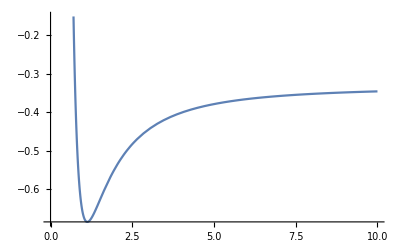

```mathematica
Plot[-1/3-1/r^2+1/r^3-1/(3 r^2),{r,0,10}]
```